## REU Formulas

We’ll need the complement of the normal distribution’s cumulutative distribution function:

```mathematica
Q[μ_,σ_]:=1.-CDF[NormalDistribution[μ,σ],u]
```

Then we can define the REU formula for each Allais gamble, with variables for the standard deviation, σ, and the power of the risk function, x:

```mathematica
REUA[σ_,x_]:=-5.+∫_-5.^5. (1.×Q[1.,σ])^x ⅆu//N
```

```mathematica
REUB[σ_,x_]:=-5.+∫_-5.^5. (.01×Q[0.,σ]+.89×Q[1.,σ]+.1×Q[2.,σ])^x ⅆu//N
```

```mathematica
REUC[σ_,x_]:=-5.+∫_-5^5. (.9×Q[0.,σ]+.1×Q[2.,σ])^x ⅆu//N
```

```mathematica
REUD[σ_,x_]:=-5.+∫_-5.^5. (.89×Q[0.,σ]+.11×Q[1.,σ])^x ⅆu//N
```

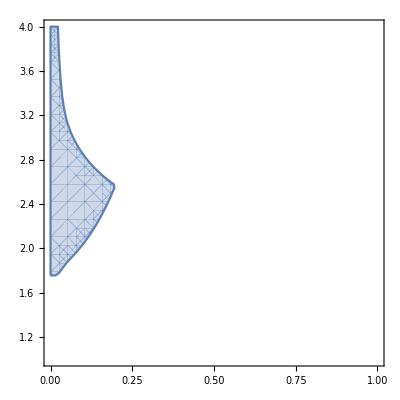

```mathematica
(* Uncomment the following code to use the (much faster) discrete model instead *)
(*
umin=-5.;
umax=5.;
udelta=.1;
pWeight[μ_,σ_,u_]:=1.-CDF[NormalDistribution[μ,σ],u-.05];
REUA[σ_,x_]:=
umin+Dot[
Table[udelta,{i,100}],
Table[
(1.0×pWeight[1,σ,u])^x
,{u,umin+udelta,umax,udelta}]
];
REUB[σ_,x_]:=
umin+Dot[
Table[udelta,{i,100}],
Table[
(.01×pWeight[0,σ,u]+.89×pWeight[1,σ,u]+.1×pWeight[2,σ,u])^x
,{u,umin+udelta,umax,udelta}]
];
REUC[σ_,x_]:=
umin+Dot[
Table[udelta,{i,100}],
Table[
(.9×pWeight[0,σ,u]+.1×pWeight[2,σ,u])^x
,{u,umin+udelta,umax,udelta}]
];
REUD[σ_,x_]:=
umin+Dot[
Table[udelta,{i,100}],
Table[
(.89×pWeight[0,σ,u]+.11×pWeight[1,σ,u])^x
,{u,umin+udelta,umax,udelta}]
];
RegionPlot[REUA[σ,x]>REUB[σ,x]&&REUC[σ,x]>REUD[σ,x],{σ,0,1},{x,1.,4.}]
*)
```

## Results at σ=.2

First we verify that, given r(p)=p^2, REU theory is risk-seeking in the grand-world context: REU(A)<REU(B) and REU(C)>REU(D).

```mathematica
REUA[.2,2.]<REUB[.2,2.]&& REUC[.2,2.]>REUD[.2,2.]
```

True

So we consider other risk functions of the form r(p)=p^x, with x ranging from 1 to 10 at .01 intervals:

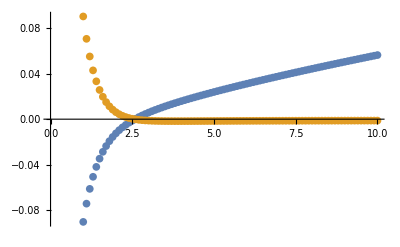

```mathematica
AminusB=Table[{x,REUA[.2,x]-REUB[.2,x]},{x,1.,10.,.01}];
CminusD=Table[{x,REUC[.2,x]-REUD[.2,x]},{x,1.,10.,.01}];
ListPlot[{AminusB,CminusD}]
```

Though it’s not immediately obvious from the graph, REU(D) overtakes REU(C) before REU(A) overtakes REU(B). We can verify this by examining the case where x=2.57:

```mathematica
REUA[.2,2.57]<REUB[.2,2.57]&&REUC[.2,2.57]<REUD[.2,2.57]
```

True

So D has become preferable to C while A has yet to become preferable to B.

Evidently, when σ=.2 there is no value of x in r(p)=p^x capable of recovering the Allais pattern.

## Results for σ>.2

We don’t expect increasing σ to help recover the Allais pattern. But just to be thorough, we check the range .2 ≤ σ ≤ 1 to see whether A might reemerge as preferable to B at some point:

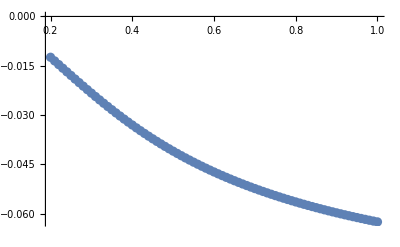

```mathematica
AminusB=Table[{σ,REUA[σ,2.]-REUB[σ,2.]},{σ,.2,1.,.01}];
ListPlot[AminusB]
```

As expected, increasing σ only decreases A’s preferability compared to B. So we turn to consider smaller values of σ instead.

## Results for σ<.2

Setting the standard deviaion to .1 doesn’t, by itself, recover the Allais pattern given r(p)=p^2. We still have REU(A)<REU(B):

```mathematica
REUA[.1,2.]<REUB[.1,2.]
```

True

But a slight increase in risk-aversion is sufficient. Just by setting r(p)=p^2.05, we recover the Allais pattern:

```mathematica
REUA[.1,2.05]>REUB[.1,2.05]&&REUC[.1,2.05]>REUD[.1,2.05]
```

True

On the other hand, too large an increase revives the problem of D being preferable to C:

```mathematica
REUC[.1,2.9]<REUD[.1,2.9]
```

True

And as σ increases, the range of successful x-values narrows. For example, at σ=.15, x has to be in a subinterval of (2.2,2.7):

```mathematica
{REUA[.15,2.2]>REUB[.15,2.2],REUC[.15,2.2]>REUD[.15,2.2]}
```

{False,True}

```mathematica
{REUA[.15,2.7]>REUB[.15,2.7],REUC[.15,2.7]>REUD[.15,2.7]}
```

{True,False}

And at σ=.19, x has to be in a subinterval of (2.5,2.6):

```mathematica
{REUA[.19,2.5]>REUB[.19,2.5],REUC[.19,2.5]>REUD[.19,2.5]}
```

{False,True}

```mathematica
{REUA[.19,2.6]>REUB[.19,2.6],REUC[.19,2.6]>REUD[.19,2.6]}
```

{True,False}

## Three σ’s: The Model

First we create a version of the discrete model with three σ-parameters, one for each normal distribution  appearing in the model.

σ0: the standard deviation for the normal distribution of mean 0 ($0)

σ1: the standard deviation for the normal distribution of mean 1 ($1 million)

σ2: the standard deviation for the normal distribution of mean 2 ($5 million)

As a result, our REU functions are now functions of three variables: σ0, σ1, σ2, and x, the power of the risk function r(p)=p^x.

```mathematica
umin=-5.;
umax=5.;
udelta=.1;
pWeight[μ_,σ_,u_]:=1.-CDF[NormalDistribution[μ,σ],u-.05];
VREUA[σ1_,x_]:=
umin+Dot[
Table[udelta,{i,100}],
Table[
(1.0×pWeight[1.,σ1,u])^x
,{u,umin+udelta,umax,udelta}]
];
VREUB[σ0_,σ1_,σ2_,x_]:=
umin+Dot[
Table[udelta,{i,100}],
Table[
(.01×pWeight[0.,σ0,u]+.89×pWeight[1.,σ1,u]+.1×pWeight[2.,σ2,u])^x
,{u,umin+udelta,umax,udelta}]
];
VREUC[σ0_,σ2_,x_]:=
umin+Dot[
Table[udelta,{i,100}],
Table[
(.9×pWeight[0.,σ0,u]+.1×pWeight[2.,σ2,u])^x
,{u,umin+udelta,umax,udelta}]
];
VREUD[σ0_,σ1_,x_]:=
umin+Dot[
Table[udelta,{i,100}],
Table[
(.89×pWeight[0.,σ0,u]+.11×pWeight[1.,σ1,u])^x
,{u,umin+udelta,umax,udelta}]
];
```

## Three σ’s: Illustration

Now, given a value for x, we can look for triples (σ0,σ1,σ2) that satisfy certain constraints. We’re looking for solutions that (1) recover the standard Allais preferences, and (2) respect the thought that more money means more financial security, hence a smaller standard deviation. So our constraints are:

VREUA[σ0,σ1,σ2,x] > VREUB[σ0,σ1,σ2,x]

VREUC[σ0,σ1,σ2,x] > VREUD[σ0,σ1,σ2,x]

σ0>σ1>σ2

We define a function “OK” that tests whether these constraints are all satisfied:

```mathematica
OK[σ0_,σ1_,σ2_,x_]:=
VREUA[σ1,x]>VREUB[σ0,σ1,σ2,x]&&VREUC[σ0,σ2,x]>VREUD[σ0,σ1,x]&&σ0>σ1>σ2
```

For example, we can verify that (σ0,σ1,σ2)=(.4,.2,.1) is not a solution when x=2.5:

```mathematica
x=2.5;σ0=.4;σ1=.2;σ2=.1;
OK[.4,.2,.1,2.5]
```

False

## Three σ’s: Initial Search

Now we step through potential values of x from 1 to 4 at invervals of 0.1. For each value of x, we generate a 3-dimensional plot of the points (σ0,σ1,σ2) that satisfy our desiderata. We let the σi range from .1 to 1, since smaller/larger values are presumably too implausible to be worth considering. This gives us an initial overview of where solutions exist:

```mathematica
Table[
RegionPlot3D[
OK[σ0,σ1,σ2,x]
,{σ0,.1,1.},{σ1,.1,1.},{σ2,.1,1.},AxesLabel->{"σ0","σ1","σ2"}
]
,{x,1.,4.,.1}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Three σ’s: Zooming In

Our initial search only turns up solutions for values of x in the range from about 2.1 to 2.7. And the solutions never seem to involve σ1>.3 or σ2>.3. So we re-run the search within these bounds to get a closer look, and with the “PlotPoints” setting fairly high to get a more accurate look at the boundaries of these regions:

```mathematica
Table[
RegionPlot3D[
OK[σ0,σ1,σ2,x]
,{σ0,.1,1.},{σ1,.1,.3},{σ2,.1,.3},
AxesLabel->{"σ0","σ1","σ2"},PlotPoints->25
]
,{x,2.0,2.7,.1}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Conclusion: there don’t seem to be any great solutions, but there are some that aren’t completely laughable. For example, when x=2.3, we can have something like (σ0,σ1,σ2)=(.8,.16,.13):

```mathematica
x=2.3;σ0=.8;σ1=.16;σ2=.13;
OK[σ0,σ1,σ2,x]
```

True